```mathematica
Get[FileNameJoin[{NotebookDirectory[],"InfiniteLists.m"}]]
```

```mathematica
InfiniteList[1,#&]
```

InfiniteList[1,#1&]

```mathematica
myInitialCondition=InfiniteList[0,If[#==0,1,0]&]
```

InfiniteList[0,If[#1==0,1,0]&]

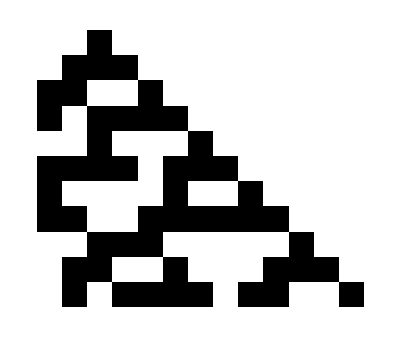

```mathematica
InfiniteCellularAutomatonPlot1[30,myInitialCondition,{-2,10},10]
```

```mathematica
myInfiniteMatrix=InfiniteMatrix[{x,y}↦ If[OddQ[x],If[EvenQ[y]&&y>x,1,0],If[OddQ[y]&&y>x,1,0]]]
```

```mathematica
myInfiniteMatrix=InfiniteMatrix[{x,y}↦ If[OddQ[x],If[EvenQ[y]&&y>x,1,0],0]]
```

InfiniteList[1,Function[x$,InfiniteList[1,Function[y$,Function[{x,y},If[OddQ[x],If[EvenQ[y]&&y>x,1,0],0]][x$,y$]]]]]

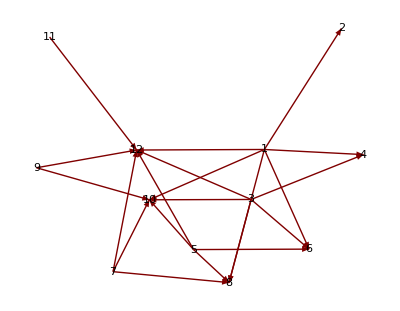

```mathematica
InfiniteTake[myInfiniteMatrix,12,12]//GraphPlot[#,VertexLabeling->True,DirectedEdges->True]&
```

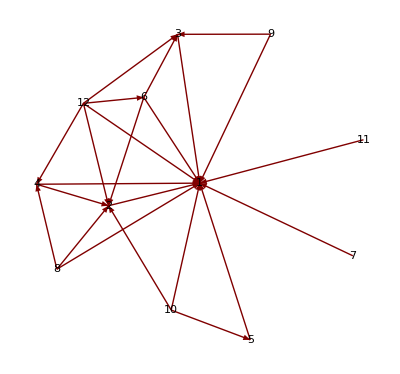

```mathematica
InfiniteTake[InfiniteMatrix[{x,y}↦If[Mod[x,y]==0,1,0]],12,12]//GraphPlot[#,VertexLabeling->True,DirectedEdges->True]&
```

```mathematica
?InfiniteCellularAutomatonPlot2
```

InfiniteLists`InfiniteCellularAutomatonPlot2

InfiniteCellularAutomatonPlot2[cellularrule_,InfiniteList[0,rule_],{n1_,n2_},t_]:=ArrayPlot[InfiniteCellularAutomatonData2[cellularrule,InfiniteList[0,rule],{n1,n2},t]]
 
InfiniteCellularAutomatonPlot2[cellularrule_,InfiniteList[0,rule_],n_,t_]:=ArrayPlot[InfiniteCellularAutomatonData2[cellularrule,InfiniteList[0,rule],n,t]]

```mathematica
InfiniteCellularAutomatonPlot2[90,InfiniteList[0,If[Mod[#,7]==0,1,0]&],40,10]
```

-Graphics-

```mathematica
InfiniteCellularAutomatonPlot1[90,InfiniteList[0,If[Mod[#,7]==0,1,0]&],40,10]
```

-Graphics-

```mathematica
InfiniteCellularAutomatonPlot1[90,InfiniteList[0,If[Mod[#,7]==0,1,0]&],15,10]
```

-Graphics-

```mathematica
InfiniteCellularAutomatonPlot1[30,InfiniteList[0,If[Mod[#,7]==0,1,0]&],15,10]
```

-Graphics-

```mathematica
myGraphMatrix=InfiniteMatrix[{x,y}↦If[Mod[x,y]==0,1,0]];
Table[GraphPlot[ 
InfiniteTake[myGraphMatrix,n,n],
VertexLabeling->True,DirectedEdges->True],
{n,3,14}]//ImageCollage[#,Background->White,Method->"Grid"]&
```

-Graphics-

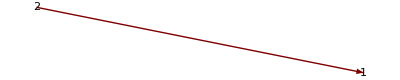
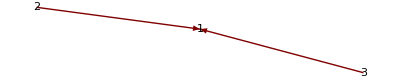
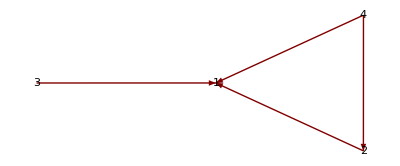
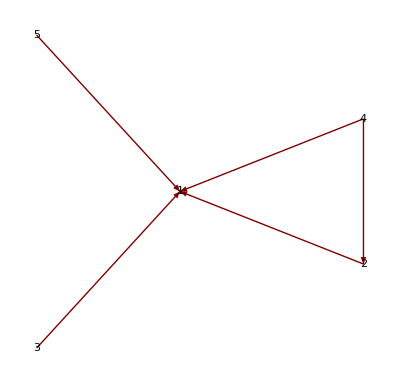
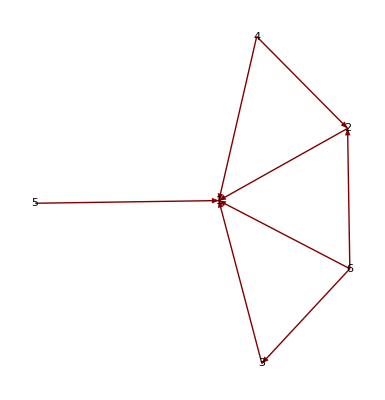
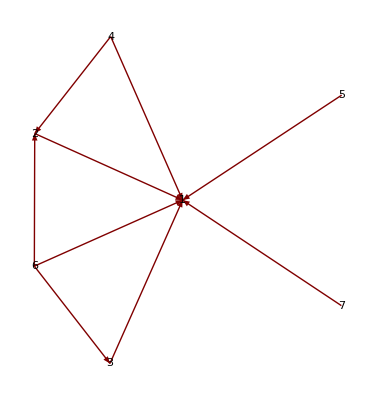
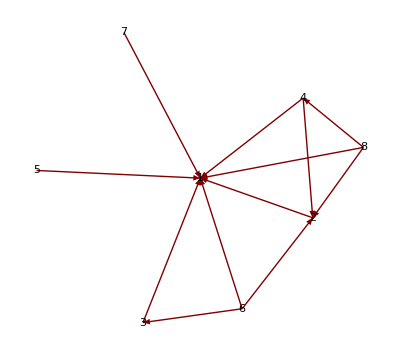
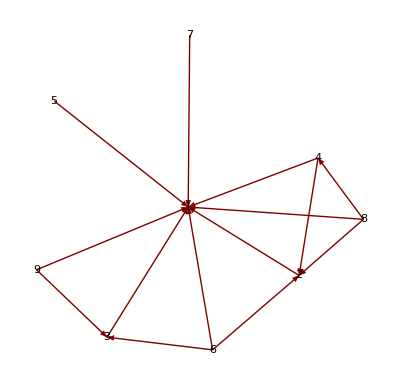
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GraphPlot[ 
InfiniteTake[myGraphMatrix,n,n],
VertexLabeling->True,DirectedEdges->True],
{n,1,14,1}]
```

```mathematica
Export["graph.gif",%7,"DisplayDurations"->1]
```

graph.gif

```mathematica
Import[%]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}